-Graphics-

# Dataset

## General Data in the Wolfram Language

-Graphics-

## 0. Summary

1. Introduction and examples

2. Structure and parts

3. Interactivity

4. Operations and queries

5. Typesetting options

6. A large example

7. Advanced topic: internal types

8. Other pointers and future plans

## 1. Introduction to Dataset

• Dataset is the Wolfram Language’s main general container for data given as nested lists and/or associations.

• General container, allows visualization, interaction and flexible queries.

• Small examples:

```mathematica
data={
<|"class"->"2nd","age"->24,"sex"->"female","survived"->False|>,
<|"class"->"1st","age"->24,"sex"->"female","survived"->True|>,
<|"class"->"3rd","age"->29,"sex"->"male","survived"->False|>,
<|"class"->"3rd","age"->20,"sex"->"male","survived"->False|>,
<|"class"->"2nd","age"->44,"sex"->"female","survived"->False|>
};
```

```mathematica
dataset=Dataset[data]
```

• Output from WL functions:

```mathematica
EntityValue[Entity["Element","Iron"],"Dataset"]
```

Or data resources:

```mathematica
ResourceData["Sample Data: Animal Weights"]
```

• Other examples we will use:

```mathematica
titanic=ExampleData[{"Dataset","Titanic"}]
```

```mathematica
planets=ExampleData[{"Dataset","Planets"}]
```

```mathematica
populations=ExampleData[{"Dataset","StatePopulations"}]
```

Dataset[<>]

## 2. Structure and parts

#### 2.1. Extract parts of a dataset

• Start from the original data:

```mathematica
data
```

{<|class→2nd,age→24,sex→female,survived→False|>,<|class→1st,age→24,sex→female,survived→True|>,<|class→3rd,age→29,sex→male,survived→False|>,<|class→3rd,age→20,sex→male,survived→False|>,<|class→2nd,age→44,sex→female,survived→False|>}

```mathematica
data[[2]]
```

<|class→1st,age→24,sex→female,survived→True|>

```mathematica
data[[2,"age"]]
```

24

```mathematica
data[[All,"age"]]
```

{24,24,29,20,44}

```mathematica
data[[{1,3,5},"age"]]
```

{24,29,44}

```mathematica
data[[2;;4,"age"]]
```

{24,29,20}

• Extract the same data from the dataset:

```mathematica
dataset
```

```mathematica
dataset[[2]]
```

```mathematica
dataset[[2,"age"]]
```

24

```mathematica
dataset[[All,"age"]]
```

```mathematica
dataset[[{1,3,5},"age"]]
```

```mathematica
dataset[[2;;4,"age"]]
```

We can also use “functional notation”, with a single pair of brackets:

```mathematica
dataset[2]
```

```mathematica
dataset[2,"age"]
```

24

• Dimensions reports the size of the rectangular part of the dataset:

```mathematica
Dimensions[dataset]
```

{5,4}

• If the part does not exist we get Failure[...] back:

```mathematica
dataset[6,"age"]
```

Failure[…]

```mathematica
dataset[5,"name"]
```

Failure[…]

#### 2.2. Visualize parts of the dataset

• Hover over the elements of the dataset and note how the parts are indicated at the bottom:

```mathematica
dataset
```

• A deeper dataset:

```mathematica
planets
```

This “matrix entry” is a matrix itself, so we have an object with maximum depth 4:

```mathematica
planets[["Mars","Moons"]]
```

```mathematica
planets[["Mars","Moons","Phobos","Radius"]]
```

11.1 km

Note that numeric indexing is always possible:

```mathematica
planets[[4,3,1,2]]
```

11.1 km

#### 2.3. Limit output dimensions

• Force scrolls bars by selecting low maximum numbers of items:

```mathematica
assoc=AssociationThread[Take[Alphabet[],10],Range[0,9]]
```

<|a→0,b→1,c→2,d→3,e→4,f→5,g→6,h→7,i→8,j→9|>

```mathematica
ds=Dataset[Association[Table[i->10i+assoc,{i,0,19}]]]
```

Use Dataset’s option MaxItems:

```mathematica
Dataset[ds,MaxItems->{4,8}]
```

#### 2.4. Restructure the dataset

• Add a new level to the structure by grouping rows with the same value of some column:

```mathematica
dataset
```

```mathematica
dataset[GroupBy[#class&]]
```

```mathematica
Normal[%]
```

<|2nd→{<|class→2nd,age→24,sex→female,survived→False|>,<|class→2nd,age→44,sex→female,survived→False|>},1st→{<|class→1st,age→24,sex→female,survived→True|>},3rd→{<|class→3rd,age→29,sex→male,survived→False|>,<|class→3rd,age→20,sex→male,survived→False|>}|>

• Same operation with the complete dataset:

```mathematica
titanic[GroupBy[#class&]]
```

## 3. Interactivity

• We have already seen scrolling and drilling down.

• Use the mouse’s right button to select one of these operations:
	Hide Column
	Sort / Reverse Sort / Unsort (for full columns)
	Copy Position/Data to Clipboard
	Paste Position/Data in New Cell

```mathematica
planets
```

• No edits currently. In progress...

## 4. Operations and queries

#### 4.1. Basic operations

• Operate on Dataset objects as standard nested WL expressions:

```mathematica
dataset
```

```mathematica
Reverse[dataset]
```

```mathematica
MapAt[ToUpperCase,dataset,{All,"sex"}]
```

#### 4.2. Query

• General concept of operation on a Dataset object:

```mathematica
Query[Reverse][dataset]
```

Act on the second level of the dataset:

```mathematica
Query[Identity,Reverse][dataset]
```

This follows Part specifications:

```mathematica
Part[dataset,{1,3,5},{"age","sex"}]
```

Idea 1: Let Query also do part extraction:

```mathematica
Query[{1,3,5},Reverse][dataset]
```

Idea 2: Use bracket notation, like Part does:

```mathematica
dataset[[{1,3,5},{"age","sex"}]]
```

```mathematica
dataset[{1,3,5},Reverse]
```

Conclusion:

	Query[op1, op2, ...][dataset] === dataset[op1, op2, ...]

where the opi can be both part specs and functions.

#### 4.3. Order of operations in a query

• Take factorials and accumulate along columns in this dataset:

```mathematica
ds=Dataset[Table[i j,{i,3},{j,4}]]
```

The operations do not commute:

```mathematica
ds[Accumulate][All,Factorial]
```

```mathematica
ds[All,Factorial][Accumulate]
```

What does this return?

```mathematica
ds[Accumulate,Factorial]
```

• For a given query with many operators:

dataset[..., op_a, ... op_b, ..., op_c, ..., op_d, ...]

classify the operators into “descending” (↓) and “ascending” (↑):

		dataset[..., op_a↓, ... op_b↑, ..., op_c↑, ..., op_d↓, ...]

and read the operators as follows:
	1) read the descending operators from left to right while descending, and then
	2) read the ascending operators from right to left while ascending:

		dataset[...][.., op_a, ..][...][.., op_d, ..][...][.., op_c, ..][...][.., op_b, ..][...]

• Classification of operators:
	“Descending”:
		- Part specs.
		- Filters like Select, SortBy, DeleteMissing.
		- GroupBy[...]
	“Ascending”:
		- Aggregation operators like Total, Mean, Catenate.
		- Arbitrary functions.
See complete rules in the [documentation page of Query].

In our example, both Accumulate and Factorial are ascending operators.

• Queries can be “compiled” into an expression that may be easier to understand:

```mathematica
Query[Accumulate,Factorial]//Normal//FullForm
```

RightComposition[Map[Factorial],Accumulate]

```mathematica
{a,b,c}//%
```

{a!,a!+b!,a!+b!+c!}

```mathematica
RightComposition[f,g,h][x]
```

h[g[f[x]]]

#### 4.4. Examples

• Simple example:

```mathematica
dataset
```

Extract the “age” column while descending and then apply Total while ascending:

```mathematica
dataset[Total,"age"]
```

141

Functions act as ascending operators, but the age is still found before computing Total:

```mathematica
dataset[Total,#age&]
```

141

• Apply an arbitrary function to all elements:

```mathematica
dataset[All,All,f]
```

• Use filters (which are descending operators):

```mathematica
dataset[Select[#age<25&],"sex"]
```

```mathematica
dataset[SortBy[#age&],KeySort]
```

• Use aggregators:

```mathematica
dataset[Counts,"class"]
```

```mathematica
titanic[Counts,"class"]
```

```mathematica
titanic[Mean,"age"]
```

15638/523

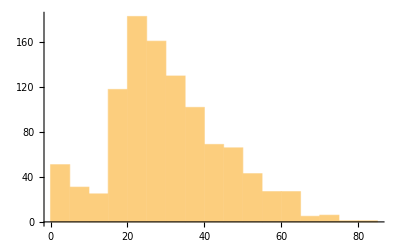

```mathematica
titanic[Histogram,"age"]
```

#### 4.5. Special case: GroupBy

• GroupBy is a descending operator that introduces a new level above the level it acts on:

```mathematica
dataset
```

```mathematica
GroupBy[dataset,#class&]
```

```mathematica
dataset[GroupBy[#class&]]
```

```mathematica
titanic[GroupBy[#class&]]
```

```mathematica
titanic[GroupBy[#class&],Histogram,"age"]
```

```mathematica
titanic[GroupBy[#class&],Around@*DeleteMissing,"age"]
```

#### 4.6. More examples

```mathematica
planets
```

```mathematica
planets[All,"Radius"]
```

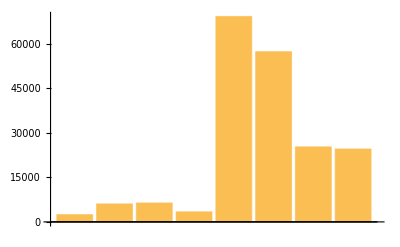

```mathematica
planets[BarChart,"Radius"]
```

Exercise: How to construct a bar-chart of densities for the eight planets?

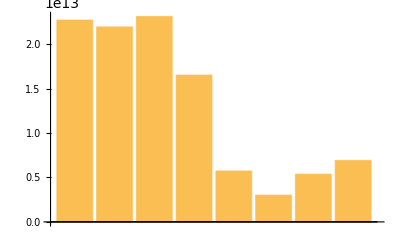

```mathematica
planets[BarChart,#Mass/#Radius^3&]
```

• Act on deeper objects:

```mathematica
planets[All,"Moons"]
```

```mathematica
planets[All,"Moons",All,"Mass"]
```

```mathematica
planets[All,"Moons",Total,"Mass"]
```

Full aggregation:

Question: Will this work?

```mathematica
planets[Total,"Moons",Total,"Mass"]
```

6.376×10^23 kg

## 5. Typesetting

### 5.1. Dataset themes

• Default typesetting of a sub-dataset of the planets example:

```mathematica
planets5=Take[planets,5]
```

#### 5.1.1. Base themes

• Basic predefined themes:

```mathematica
Dataset[planets5,DatasetTheme->"Classic"]
```

```mathematica
Dataset[planets5,DatasetTheme->"Business"]
```

```mathematica
Dataset[planets5,DatasetTheme->"Detailed"]
```

```mathematica
Dataset[planets5,DatasetTheme->"Marketing"]
```

```mathematica
Dataset[planets5,DatasetTheme->"Minimal"]
```

```mathematica
Dataset[planets5,DatasetTheme->"Monochrome"]
```

```mathematica
Dataset[planets5,DatasetTheme->"Scientific"]
```

```mathematica
Dataset[planets5,DatasetTheme->"Web"]
```

#### 5.1.2. Feature themes

• These can be combined.

• Font feature themes:
	“Bold” / “BoldHeaders” / “BoldItems”
	“Italic” / “Sans” / “Serif”
	“Large” / “Small”
	“StrongHeaders” / “WeakHeaders”

```mathematica
Dataset[planets5,DatasetTheme->{"Italic","Bold"}]
```

• Divider feature themes:
	“RowDividers” / “ColumnDividers”
	“GroupDividers” / “FullDividers”

```mathematica
Dataset[planets5,DatasetTheme->"ColumnDividers"]
```

• Background feature themes:
	“AlternatingRowBackgrounds” / “AlternatingColumnBackgrounds”
	“AlternatingRowColumnBackgrounds”
	“AlternatingLeafRowItemBackgrounds”
	“AlternatingAllRowBackgrounds”

```mathematica
Dataset[planets5,DatasetTheme->"AlternatingLeafRowItemBackgrounds"]
```

• Layout feature themes:

```mathematica
Dataset[dataset,DatasetTheme->"VerticalColumnHeaders"]
```

### 5.2. Specific typesetting options

• Default typesetting of our example dataset:

```mathematica
dataset
```

#### 5.2.1. Background / HeaderBackground

• Make all item backgrounds pink:

```mathematica
Dataset[data,Background->Pink]
```

• Choose the colors of the respective rows or columns:

```mathematica
Dataset[data,Background->{Pink,Yellow}]
```

```mathematica
Dataset[data,Background->{None,{Pink,Yellow}}]
```

```mathematica
Dataset[data,Background->{{{Pink,Yellow}},{{Blue,Green}}}]
```

• Alternate colors:

```mathematica
Dataset[data,Background->{{{Pink,Gray}}}]
```

• Specify the background style for individual items:

```mathematica
Dataset[data,Background->{{2,"age"}->Pink,{4,"survived"}->Yellow}]
```

```mathematica
Dataset[data,Background->{{All,"survived"}->Yellow,{2}->Pink}]
```

• Use patterns in positions:

```mathematica
Dataset[IdentityMatrix[5],Background->{{2|4,_?OddQ}->Pink}]
```

• Set background color by value:

```mathematica
Dataset[IdentityMatrix[5],Background->(If[#1===1,Pink,White]&)]
```

• Set background color by position:

```mathematica
Dataset[IdentityMatrix[5],Background->(If[Total[#2]<6,Pink,White]&)]
```

• Set background colors of headers:

```mathematica
Dataset[planets,HeaderBackground->{Pink,Cyan,Green,Orange}]
```

#### 5.2.2. Alignment / HeaderAlignment

• By default Dataset uses left-alignment. Change to right-alignment:

```mathematica
Dataset[data,Alignment->Right]
```

```mathematica
Dataset[data,Alignment->{"sex"->Right}]
```

```mathematica
Dataset[data,Alignment->{Right,"sex"->Left}]
```

• Control header alignment:

```mathematica
Dataset[planets,HeaderAlignment->{{Center,{Top,Bottom}},Right}]
```

#### 5.2.3. ItemSize / HeaderSize

• Select item sizes:

```mathematica
Dataset[data,ItemSize->2]
```

```mathematica
Dataset[data,ItemSize->{10,4}]
```

• Select the size of the second row:

```mathematica
Dataset[data,ItemSize->{{2}->{Automatic,4}}]
```

• Specify header sizes:

```mathematica
Dataset[data,HeaderSize->{10,4}]
```

#### 5.2.4. ItemStyle / HeaderStyle

• Select the style of the items data:

```mathematica
Dataset[data,ItemStyle->"Subsubsubsubsection"]
```

• Specify individual styles:

```mathematica
Dataset[data,ItemStyle->{{2,"survived"}->Red,{5,"age"}->Underlined}]
```

• Specify the header styles:

```mathematica
Dataset[data,HeaderStyle->Bold]
```

#### 5.2.5. ItemDisplayFunction / HeaderDisplayFunction

• Give a full specification of how the data should be displayed:

```mathematica
Dataset[data,ItemDisplayFunction->{"sex"->(If[#==="male","♀","♂"]&)}]
```

Only the display was modified, not the data itself:

```mathematica
%//Normal
```

{<|class→2nd,age→24,sex→female,survived→False|>,<|class→1st,age→24,sex→female,survived→True|>,<|class→3rd,age→29,sex→male,survived→False|>,<|class→3rd,age→20,sex→male,survived→False|>,<|class→2nd,age→44,sex→female,survived→False|>}

• Specify how the headers should be displayed:

```mathematica
Dataset[data,HeaderDisplayFunction->(ToUpperCase[#]&)]
```

## 6. A large example

• Download covid data from the NYTimes:

```mathematica
AbsoluteTiming[ByteCount[
covid=Import["https://raw.githubusercontent.com/nytimes/covid-19-data/master/us-counties.csv","Dataset"]
]]
```

{27.5168,642195712}

There are more than 2.5 million lines:

```mathematica
Dimensions[covid]
```

{2502833,6}

```mathematica
covid
```

Dataset[<>]

```mathematica
covid3=covid[GroupBy[#[[1]]&],GroupBy[#[[3]]&],GroupBy[#[[2]]&]]
```

Dataset[<>]

Number of dates:

```mathematica
Length[covid3]
```

845

Number of states:

```mathematica
Length[covid3["2022-05-13"]]
```

56

Number of counties:

```mathematica
Length[covid3["2022-05-13","Illinois"]]
```

103

Number of values in the table for Champaign IL that date:

```mathematica
Length[covid3["2022-05-13","Illinois","Champaign"]]
```

1

```mathematica
covid3["2022-05-13","Illinois","Champaign",1]
```

```mathematica
covidChampaign=DeleteMissing[covid3[All,"Illinois","Champaign",1]]
```

Number of cases since March 22, 2020:

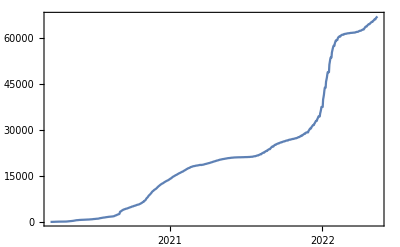

```mathematica
covidChampaign[DateListPlot,5]
```

Number of deaths:

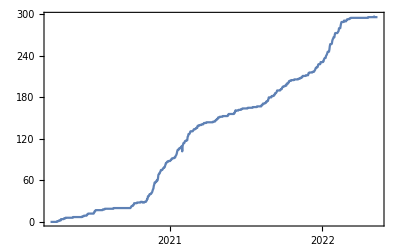

```mathematica
covidChampaign[DateListPlot,6]
```

## 7. Advanced topic: internal structure

• Let us look at the internal structure of Dataset objects.

• There are three arguments:
	data
	type
	options

```mathematica
Dataset[dataset,Background->LightBlue]
```

```mathematica
%//InputForm
```

Dataset[{<|"class" -> "2nd", "age" -> 24, "sex" -> "female", 
   "survived" -> False|>, <|"class" -> "1st", "age" -> 24, 
   "sex" -> "female", "survived" -> True|>, 
  <|"class" -> "3rd", "age" -> 29, "sex" -> "male", 
   "survived" -> False|>, <|"class" -> "3rd", "age" -> 20, 
   "sex" -> "male", "survived" -> False|>, 
  <|"class" -> "2nd", "age" -> 44, "sex" -> "female", 
   "survived" -> False|>}, TypeSystem`Vector[
  TypeSystem`Struct[{"class", "age", "sex", "survived"}, 
   {TypeSystem`Atom[TypeSystem`Enumeration["1st", "2nd", 
      "3rd"]], TypeSystem`Atom[Integer], 
    TypeSystem`Atom[TypeSystem`Enumeration["female", "male"]], 
    TypeSystem`Atom[TypeSystem`Boolean]}], 5], 
 <|Background -> RGBColor[0.87, 0.94, 1]|>]

```mathematica
Dataset[
{
<|"class" -> "2nd", "age" -> 24, "sex" -> "female", "survived" -> False|>, 
<|"class" -> "1st", "age" -> 24, "sex" -> "female", "survived" -> True|>,
<|"class" -> "3rd", "age" -> 29, "sex" -> "male", "survived" -> False|>,
<|"class" -> "3rd", "age" -> 20, "sex" -> "male", "survived" -> False|>,
<|"class" -> "2nd", "age" -> 44, "sex" -> "female", "survived" -> False|>
},
TypeSystem`Vector[
TypeSystem`Struct[
{"class", "age", "sex", "survived"},
{TypeSystem`Atom[TypeSystem`Enumeration["1st", "2nd", "3rd"]],
 TypeSystem`Atom[Integer],
TypeSystem`Atom[TypeSystem`Enumeration["female", "male"]],
 TypeSystem`Atom[TypeSystem`Boolean]}
],
 5
],
<|Background -> RGBColor[0.87, 0.94, 1]|>
]
```

## 8. Conclusions and future plans

• Dataset is a general purpose data container in Wolfram Language.

• It offers useful visualization of the data and its structure, allowing much interaction and detailed specification of the final appearance.

• The Query language of Dataset allows powerful manipulation, restructuring and analysis of the data, merging the systematic Part specification with the flexible functional approach of the Wolfram Language.

• In the future we want to extend the framework to allow even more interaction, in particular data editing. We also want to improve the internal storage methods to make Dataset faster and capable of handling very large amounts of data.